```mathematica
ClearAll[sol,kappa,T0,Ptot,Pbkg,A,r,θ,z,x,y,z0,sr,sz,Lzrad,Rrad,CrossSection,Rstick,Lstick,NormIntegral, powerDensity3DFunc,powerDensity3D,copperCylinderRegion,copperStickRegion,copperRegion,meshRegion];
```

```mathematica
$Assumptions=Lstick∈Reals&&Lstick>0 && Rstick∈Reals&& Rstick>0 && z0∈Reals&&z0≥0&&z0≤Lstick;
```

```mathematica
(*powerDensity3DFunc[r_,θ_,z_]:=Piecewise[{{Exp[-(r^2/(2*sr^2))], z≥z0}},0];*)
```

```mathematica
powerDensity3DFunc[r_,θ_,z_]:=Piecewise[{{1.0, z≥z0&&z≤Lstick}},0];
```

```mathematica
NormIntegral=Integrate[r*powerDensity3DFunc[r,θ,z],{r,0,Rstick},{θ,0,+2π},{z,0, Lstick}]
```

Piecewise[{{3.14159 Lstick Rstick^2, Lstick>0.&&Rstick>0.&&z0==0.}, {3.14159 Rstick^2 (Lstick-1. z0), Lstick>0.&&Rstick>0.&&z0>0.&&Lstick-1. z0>0.}, {0., True}}]

```mathematica
kappa=0.00385;T0=50.0;Ptot=0.015;CrossSection=2.0;
(*Lzrad=0.15;*)Lzrad=1;Rrad=1.0;
Rstick=(CrossSection/π)^(1/2);Lstick=100;
z0=Lstick-1;sr=10;sz=0.05;
```

```mathematica
NormIntegral
```

2.

```mathematica
N[Rstick]
```

0.797885

```mathematica
powerDensity3D[r_,θ_,z_]:=Ptot/NormIntegral*powerDensity3DFunc[r,θ,z]
```

```mathematica
NIntegrate[r*powerDensity3D[r,θ,z],{r,0,Rstick},{θ,0,+2π},{z,0, Lstick}]
```

0.015

```mathematica
Ptot/NormIntegral
```

0.0075

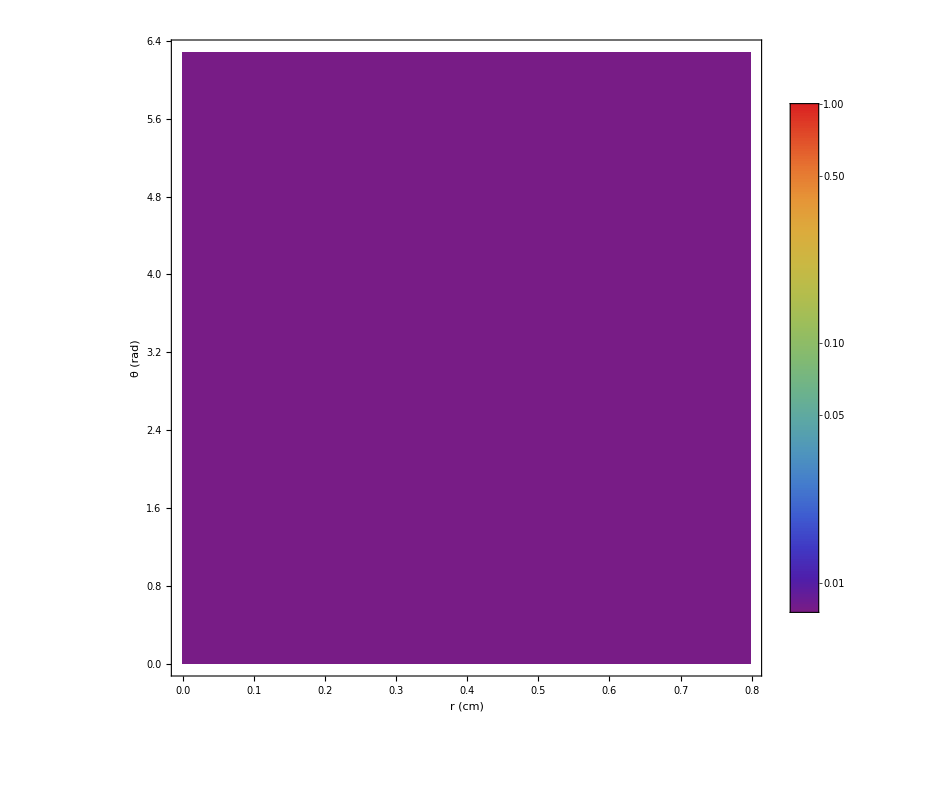

```mathematica
DensityPlot[powerDensity3D[r,θ,z0],{r,0,Rstick},{θ,0,+2π},ColorFunction->{"Rainbow"},PlotRange->Full,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"r (cm)","θ (rad)","\!\(\*FractionBox[\(ΔE\), \(ΔV\)]\) (\!\(\*FractionBox[\(KW\), \(\(\\\ \)\*SuperscriptBox[\(cm\), \(3\)]\)]\) )"},LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

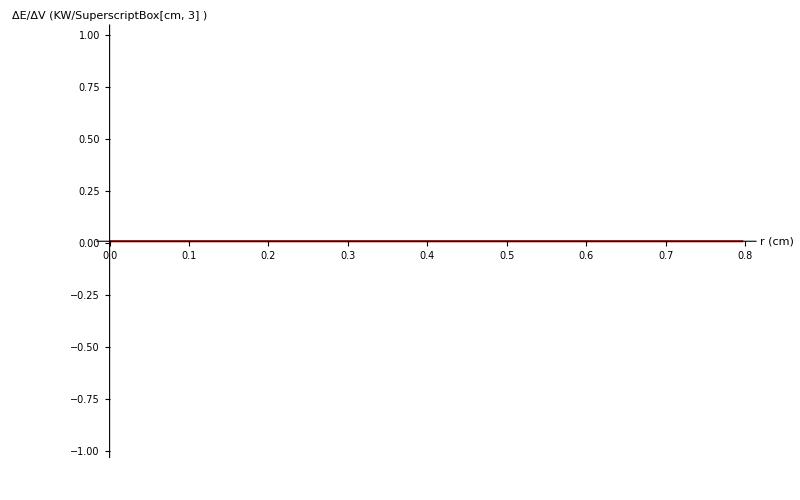

```mathematica
Plot[powerDensity3D[r,0,z0],{r,0,Rstick},AxesLabel->{"r (cm)","\!\(\*FractionBox[\(ΔE\), \(ΔV\)]\) (\!\(\*FractionBox[\(KW\), \(\(\\\ \)\*SuperscriptBox[\(cm\), \(3\)]\)]\) )"},LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full,PlotStyle->{Red,Thickness[0.002]}]
```

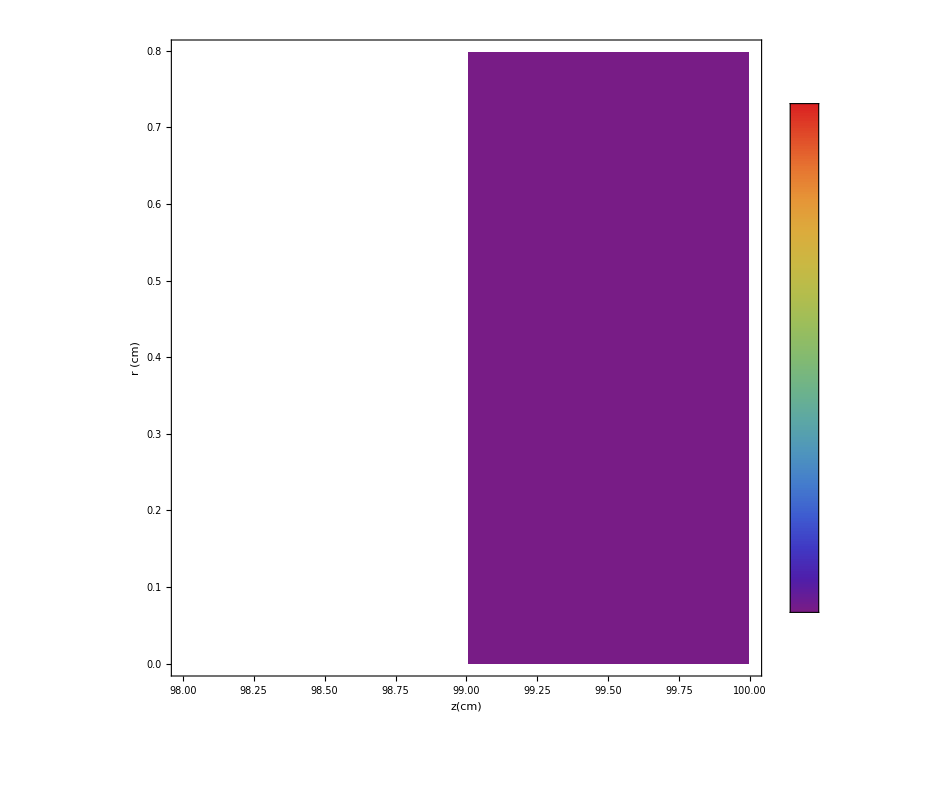

```mathematica
DensityPlot[powerDensity3D[r,0,z],{z,98,Lstick},{r,0,Rstick},ColorFunction->"Rainbow",PlotRange->Full,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"z(cm)","r (cm)","\!\(\*FractionBox[\(ΔE\), \(ΔV\)]\) (\!\(\*FractionBox[\(KW\), \(\(\\\ \)\*SuperscriptBox[\(cm\), \(3\)]\)]\) )"},LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

```mathematica
eqn=-Laplacian[u[r,θ, z],{r,θ, z}, "Cylindrical"]==1/kappa*powerDensity3D[r,θ, z] + NeumannValue[0, r==Rstick]
```

-u^(0,0,2)[r,θ,z]-((u^(0,2,0)[r,θ,z])/r+u^(1,0,0)[r,θ,z])/r-u^(2,0,0)[r,θ,z]==NeumannValue[0,r==0.797885]+1.94805 (Piecewise[{{1., z≥99&&z≤100}, {0, True}}])

```mathematica
(*eqn=-Laplacian[u[r,θ, z],{r,θ, z}, "Cylindrical"]==1/kappa*powerDensity3D[r,θ, z];*)
```

```mathematica
(*eqn=-Laplacian[u[r, z],{r,z}]==NeumannValue[0, r==Rstick]*)
```

```mathematica
(*sol=DSolve[{eqn,{u[r,θ, 0]==T0, u[r,θ, Lstick]==200}},u,{r,θ, z} ]*)
```

```mathematica
sol=NDSolveValue[{eqn,{u[r, θ,0]==T0}},u,{r,0, Rstick}, {θ,0,+2π},{z, 0, Lstick},MaxStepSize->0.0001,AccuracyGoal->100,PrecisionGoal->100]
```

InterpolatingFunction[{{0., 0.797885}, {0., 6.28319}, {0., 100.}}, <>]

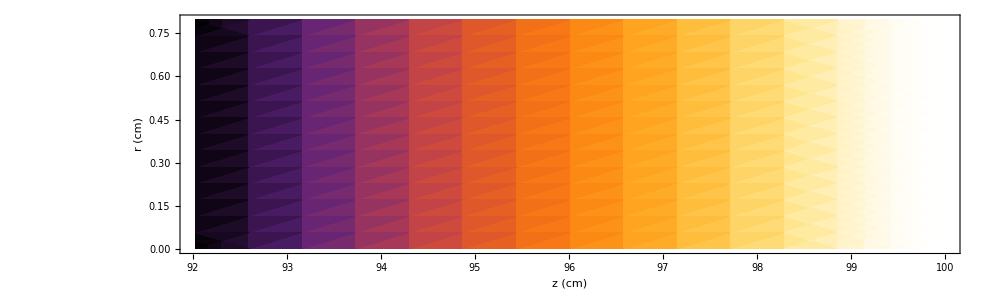

```mathematica
DensityPlot[sol[r,0,z],{z,Lstick-10*Rstick,Lstick},{r,0,Rstick},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->Full,ImageSize->{1000,400},FrameLabel->{"z (cm)","r (cm)","T \!\(\*SuperscriptBox[\((\), \(o\)]\)C)"},LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->0.3]
```

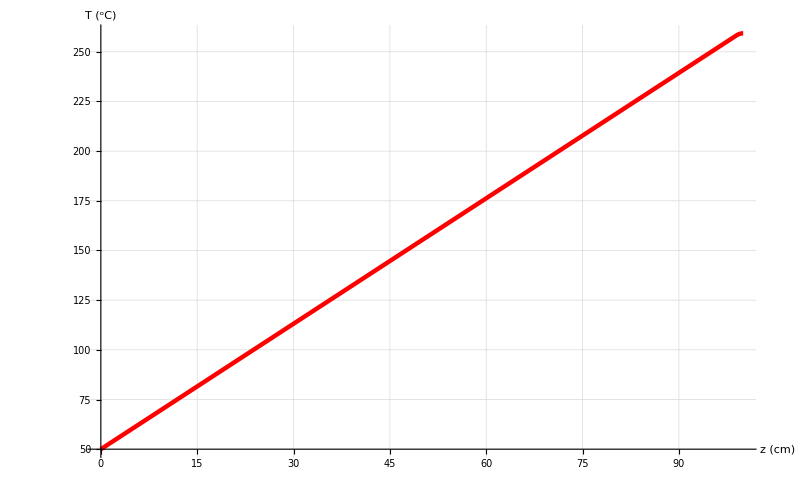

```mathematica
Plot[sol[0,0,z], {z,0, Lstick},GridLines->Automatic,PlotRange->Full,AxesLabel->{"z (cm)","T \!\(\*SuperscriptBox[\((\), \(o\)]\)C)"},LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotStyle->{Red,Thickness[0.004]}]
```

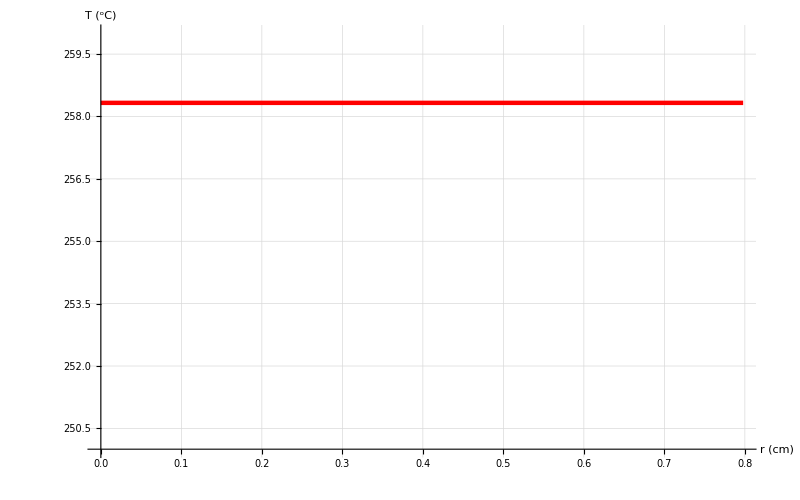

```mathematica
Plot[sol[r,0,z0], {r,0, Rstick},GridLines->Automatic,PlotRange->{250,260},AxesLabel->{"r (cm)","T \!\(\*SuperscriptBox[\((\), \(o\)]\)C)"},LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotStyle->{Red,Thickness[0.004]}]
```

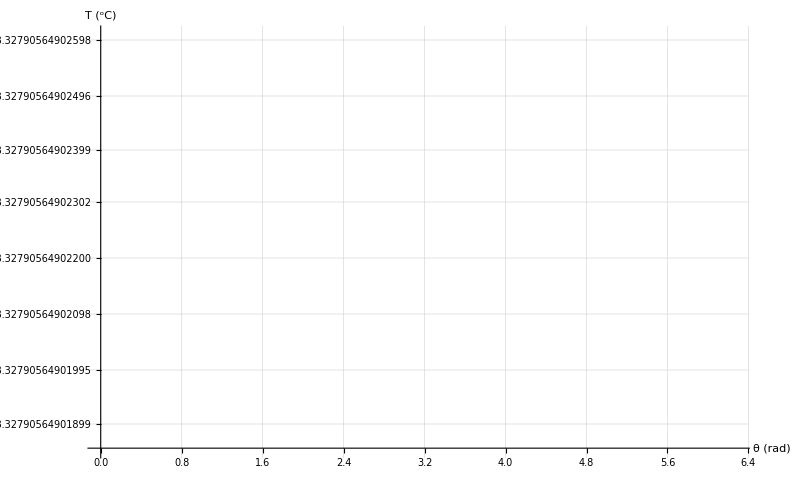

```mathematica
Plot[sol[Rstick/2,θ,z0], {θ,0, 2π},GridLines->Automatic,PlotRange->Full,AxesLabel->{"θ (rad)","T \!\(\*SuperscriptBox[\((\), \(o\)]\)C)"},LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotStyle->{Red,Thickness[0.004]}]
```